ToDo:  
Figure out how to choose beta.  One idea is that we balance the contribution of the non-beta term with the beta term so that each contributes equally to the reward function (easy to do).  A more convincing method would be to find a point where the policy is halfway between the beta=0 and beta=large policies (not so easy).

Try to add new features and remove features.  This must be done after we settle on value for beta.  Use correlation matrix for states to determine best candidates for removal.

Need to think of a way to decide if logistic or step is better for fitting.  Logistic gives a better value for reward (of course).  But does this buy us anything?  In the case of step, then there is an extra overall scale that can be removed from each policy.  We should maybe add a constraint or extra term in the reward to fit that policy.

Eventually (after first iteration), need to figure out when random-help policy should be applied.  If we only choose optimal help based on current best guess, we may not explore parts of policy-space vs. state that need exploring.  As we increase the amount of data, the fraction of time we use the random policy should decrease.  We need some estimate of the probability that the second-best policy is, in fact, the best policy.

### State

```mathematica
Dimensions[state=Import["state-uwplatt.csv"]]
```

{15327,10}

```mathematica
state[[1]]
```

{ttID,logSessionTime,fracSessionFlounderTime,logNowFlounderSteps,logNowFlounderTime,logNowStepTime,sessionCorrect,sessionIncorrect,sessionHelp,fracSessionCorrect}

Create hash table for fast lookup

```mathematica
Map[(state1[#[[1]]]=Rest[#])&,Rest[state]];
nFeatures=Length[Rest[state[[1]]]]
```

9

### Reward

```mathematica
Dimensions[reward=Import["reward-md5:e2ed3385.csv"]]
```

{59,10}

```mathematica
Dimensions[reward=Import["reward-uwplatt-2Y130.csv"]]
```

{812,12}

```mathematica
Dimensions[reward=Import["reward-uwplatt.csv"]]
```

{7210,12}

```mathematica
reward[[1]]
```

{KC,clientID,ttID,learning,slipTurns,slip,spontaneous-hint,no-hints,GIVE-BACKWARDS-HINTS,forwards-hint,zz-unclassified-hint,zz-extra-hint}

### Evaluate State & Reward

```mathematica
Map[Histogram[Rest[#],PlotLabel->First[#],PlotRange->All]&,Transpose[Map[Rest,state]]]
```

```mathematica
TableForm[Correlation[Map[Rest,Rest[state]]],TableHeadings->{Rest[state[[1]]],Rest[state[[1]]]}]
```

| logSessionTime | fracSessionFlounderTime | logNowFlounderSteps | logNowFlounderTime | logNowStepTime | sessionCorrect | sessionIncorrect | sessionHelp | fracSessionCorrect
logSessionTime | 1. | 0.651338 | 0.311562 | 0.301274 | 0.0736642 | 0.721848 | 0.642297 | 0.501846 | -0.417251
fracSessionFlounderTime | 0.651338 | 1. | -0.0575093 | -0.0696664 | -0.0705747 | 0.428488 | 0.477 | 0.32602 | -0.370403
logNowFlounderSteps | 0.311562 | -0.0575093 | 1. | 0.962906 | 0.0545284 | 0.0111198 | 0.26894 | 0.192042 | -0.476544
logNowFlounderTime | 0.301274 | -0.0696664 | 0.962906 | 1. | 0.109902 | 0.00164358 | 0.22699 | 0.139857 | -0.45948
logNowStepTime | 0.0736642 | -0.0705747 | 0.0545284 | 0.109902 | 1. | -0.0444632 | -0.0232201 | -0.150746 | -0.0172625
sessionCorrect | 0.721848 | 0.428488 | 0.0111198 | 0.00164358 | -0.0444632 | 1. | 0.661039 | 0.489532 | -0.0344468
sessionIncorrect | 0.642297 | 0.477 | 0.26894 | 0.22699 | -0.0232201 | 0.661039 | 1. | 0.397376 | -0.319528
sessionHelp | 0.501846 | 0.32602 | 0.192042 | 0.139857 | -0.150746 | 0.489532 | 0.397376 | 1. | -0.26693
fracSessionCorrect | -0.417251 | -0.370403 | -0.476544 | -0.45948 | -0.0172625 | -0.0344468 | -0.319528 | -0.26693 | 1.

List different policy combinations and number of instances of each

```mathematica
Block[{pp=Map[Drop[#,6]&,Rest[reward]]},Map[{#,Count[pp,#]}&,Union[pp]]]
```

{{{0,0,0,0,0,1},1},{{0,0,0,0,1,0},19},{{0,0,0,1,0,0},33},{{0,0,1,0,0,0},17},{{0,1,0,0,0,0},459},{{1,0,0,0,0,0},236},{{1,0,0,0,1,0},46}}

### Analyze routines

Policy choice is represented by a 0 or 1; -1 means policy doesn' t apply.  There is some nonsense in Budinich paper about -1 & 1 being preferred, but Eqn. (2) in paper is effectively the same for either convention.

```mathematica
Clear[rewardPosition];rewardPosition[x_]:=rewardPosition[x]=First[First[Position[reward[[1]],x,1,1]]];
rewardValue[x_,y_]:=x[[rewardPosition[y]]]
```

```mathematica
policyVector[x_]:={Which[rewardValue[x,"no-hints"]==1,0,rewardValue[x,"spontaneous-hint"]==1,1,True,-1],
Which[rewardValue[x,"GIVE-BACKWARDS-HINTS"]==1,1,rewardValue[x,"forwards-hint"]==1,0,True,-1]};
nPolicies=2;  (* Number of policies *)
comparePolicies[x_,y_]:=If[x===-1||y===-1,0,(x-y)^2] (* For policy to not apply, -1 must be explicit *);
comparePolicyVectors[x_,y_]:=Inner[comparePolicies,x,y,Plus];
invertPolicyVector[x_]:=Map[If[#<0,#,1-#]&,x]
```

```mathematica
signedDistance[state_,x_]:=Block[{b=Take[x,-2],a=Partition[Drop[x,-2],nFeatures]},Table[(a[[i]].state+b[[i]])/Sqrt[a[[i]].a[[i]]],{i,Length[b]}]]
linearPolicy[state_,x_,which_:True]:=Map[If[(* Choose between step function and a logistic *) which,(Sign[#]+1)/2,(Tanh[#/2]+1)/2]&,signedDistance[state,x]]
```

Maybe should have weight for integrated probability (probability student has already learned skill before this step).

```mathematica
rewardFunctionTerm[x_,beta_,r_]:= 
Block[{pp=linearPolicy[state1[r[[3]]],x]},(r[[4]]+If[r[[5]]>0 ,beta (1-r[[6]])/r[[5]],0])comparePolicyVectors[pp,policyVector[r]]+If[r[[5]]>0,beta r[[6]]/r[[5]],0] comparePolicyVectors[pp,invertPolicyVector[policyVector[r]]]];
rewardFunction[x_,beta_]:=Apply[Plus,Map[rewardFunctionTerm[x,beta,#]&,Rest[reward]]]
```

```mathematica
minit1[beta_,opts___]:=Block[{xx=Table[x[i],{i,nPolicies*(1+nFeatures)}],zz},
zz=NMinimize[rewardFunction[xx,beta],xx,opts];{First[zz],xx/.zz[[2]]}];
minit2[beta_,opts___]:=Block[{xx=Table[x[i],{i,nPolicies*(1+nFeatures)}],yy,zz},yy=Map[{#,(Random[]-0.5)*10}&,xx];zz=FindMinimum[rewardFunction[xx,beta],yy,opts];{First[zz],xx/.zz[[2]]}]
```

Count, for each step where a policy choice can be made, number of instances of each policy choice or pair of policy choices.  If input is not a list, use original choice taken by Andes.

```mathematica
getPolicyVector[x_,r_]:=If[Head[x]===List,linearPolicy[state1[r[[3]]],x],policyVector[r]];
dist[x_]:=Block[{y=Map[getPolicyVector[x,#]&,Rest[reward]]},TableForm[Map[Count[y,#]&,Union[y]],TableHeadings->{Union[y],None}]];
dist[x_,y_]:=Block[{z=Map[{getPolicyVector[x,#],getPolicyVector[y,#]}&,Rest[reward]],hx,hy},hx=Union[Map[#[[1]]&,z]];hy=Union[Map[#[[2]]&,z]];TableForm[Outer[Count[z,{#1,#2}]&,hx,hy,1],TableHeadings->{hx,hy}]]
```

### Analyze

Calculate random data point

```mathematica
rewardFunction[Table[(Random[]-0.5)*10,{nPolicies*(1+nFeatures)}],1.0]
```

227.058

```mathematica
Timing[soln1=minit1[1.0]]
```

{6.42002,{45.2006,{0.37707,0.774106,1.1428,-0.582141,1.14073,0.126489,-1.33669,1.6332,0.344965,-0.0537927,-1.14837,-0.601895,-0.679338,0.690493,-1.94286,-0.333572,0.470441,0.117084,-0.20212,-1.99375}}}

```mathematica
Timing[soln2=minit1[1.0]]
```

{39.308,{27.343,{-1.31467,0.957805,-0.917242,0.283947,0.346319,0.313899,-0.0550646,0.154001,-3.4589,0.537298,-0.693554,-3.11662,1.49322,-2.18267,-1.40101,0.373129,-0.204422,-0.765734,4.95892,3.27354}}}

```mathematica
dist[0]
```

{-1,-1} | 299
{-1,0} | 566
{-1,1} | 176
{0,-1} | 3685
{1,-1} | 2066
{1,0} | 361
{1,1} | 56

### Different values of beta (step)

#### Calculate solutions

```mathematica
Timing[soln[0]=minit1[0,Method->"DifferentialEvolution"]]
```

{98.879,{43.1818,{-1.38524,2.54552,-1.19313,-0.0336265,1.12021,0.76911,-1.04034,0.563675,1.16718,-0.456857,-0.0618504,-0.50904,0.205767,0.32004,0.167733,-1.65905,-0.29185,2.33904,-0.493267,-1.36973}}}

```mathematica
Timing[soln[1/8]=minit1[0.125,Method->"DifferentialEvolution"]]
```

{332.198,{63.9907,{-2.92384,6.53361,5.45488,0.176616,2.09537,2.26036,-3.49745,0.38257,-0.203968,-3.0381,1.7474,1.30887,2.94072,-4.23367,-1.91724,-0.23893,-2.67859,-3.14579,3.769,-4.36144}}}

```mathematica
Timing[soln[1/4]=minit1[0.25,Method->"DifferentialEvolution"]]
```

{375.62,{84.6661,{-0.103266,-0.258985,0.787679,-1.34879,-3.99166,-1.48589,0.221579,2.04327,1.01853,-0.932197,-2.29089,-0.489914,-2.92848,-2.82509,0.826112,-0.725467,-5.54207,0.525163,-2.72891,3.9319}}}

```mathematica
Timing[soln[1/2]=minit1[0.5,Method->"DifferentialEvolution"]]
```

{473.012,{124.606,{-3.05576,5.67502,-2.60593,-0.985362,-6.78051,-1.24147,-0.283063,4.86904,-2.62823,-0.801886,0.647688,1.02356,0.305808,1.03789,-1.5123,-0.766073,1.20873,2.00369,-2.61421,-2.07383}}}

```mathematica
Timing[soln[1]=minit1[1.0,Method->"DifferentialEvolution"]]
```

{273.263,{206.817,{-0.924848,-3.36765,0.112674,-0.813309,-3.58728,-0.0312991,-0.0529553,2.41469,0.715368,0.103787,6.10261,-0.909421,1.91174,-3.07808,-0.187132,-2.30592,1.22858,1.04314,1.40137,-0.78147}}}

```mathematica
Timing[soln[2]=minit1[2.0,Method->"DifferentialEvolution"]]
```

{40.0439,{80.1905,{-0.743854,4.04323,-0.933968,0.763812,0.845472,0.533912,-1.65108,3.73145,-2.02975,-0.883294,1.38203,-1.61604,1.00414,-0.192099,-0.95835,-0.850945,-1.99308,0.995841,1.04454,-2.26748}}}

```mathematica
Timing[soln[4]=minit1[4.0,Method->"DifferentialEvolution"]]
```

{44.8022,{150.377,{0.916824,-1.55574,-4.50516,1.11846,1.21694,-0.652365,-1.35357,3.99325,2.33894,-1.68031,1.97212,-2.40803,-0.13557,2.37946,-2.57776,-10.8149,0.818853,1.6902,-4.00724,1.08482}}}

```mathematica
betaList={0,1/8,1/4,1/2,1,2,4};
```

```mathematica
Save["soln-uwplatt.m",{soln,betaList}]
```

#### Analyze Solutions

```mathematica
Get["soln-uwplatt-2Y130.m"];
```

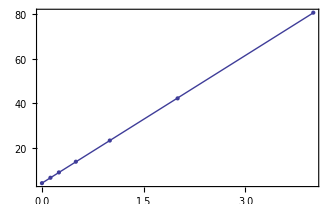

```mathematica
Block[{pp=Map[{#,First[soln[#]]}&,betaList],y},y=Fit[pp,{1,x},x];Show[ListPlot[pp,PlotRange->All,Axes->False,Frame->True],Plot[y,{x,0,4}]]]
```

```mathematica
Map[{#,soln[#][[1]],dist[soln[#][[2]]]}&,betaList]
```

{{0,4.04049,{0,0} | 635
{0,1} | 8
{1,0} | 165
{1,1} | 3},{1/8,6.47643,{0,0} | 637
{0,1} | 16
{1,0} | 155
{1,1} | 3},{1/4,8.87538,{0,0} | 658
{0,1} | 1
{1,0} | 152},{1/2,13.6842,{0,0} | 657
{0,1} | 6
{1,0} | 147
{1,1} | 1},{1,23.1982,{0,0} | 645
{1,0} | 166},{2,42.155,{0,0} | 641
{0,1} | 7
{1,0} | 163},{4,80.6818,{0,0} | 544
{1,0} | 267}}

Compare solutions for different beta values

```mathematica
Map[{#,dist[soln[0][[2]],soln[#][[2]]]}&,betaList]
```

{{0, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 635 | 0 | 0 | 0
{0,1} | 0 | 8 | 0 | 0
{1,0} | 0 | 0 | 165 | 0
{1,1} | 0 | 0 | 0 | 3},{1/8, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 619 | 14 | 2 | 0
{0,1} | 6 | 2 | 0 | 0
{1,0} | 12 | 0 | 153 | 0
{1,1} | 0 | 0 | 0 | 3},{1/4, | {0,0} | {0,1} | {1,0}
{0,0} | 624 | 0 | 11
{0,1} | 8 | 0 | 0
{1,0} | 25 | 0 | 140
{1,1} | 1 | 1 | 1},{1/2, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 627 | 6 | 2 | 0
{0,1} | 8 | 0 | 0 | 0
{1,0} | 22 | 0 | 143 | 0
{1,1} | 0 | 0 | 2 | 1},{1, | {0,0} | {1,0}
{0,0} | 624 | 11
{0,1} | 8 | 0
{1,0} | 13 | 152
{1,1} | 0 | 3},{2, | {0,0} | {0,1} | {1,0}
{0,0} | 609 | 7 | 19
{0,1} | 7 | 0 | 1
{1,0} | 25 | 0 | 140
{1,1} | 0 | 0 | 3},{4, | {0,0} | {1,0}
{0,0} | 526 | 109
{0,1} | 8 | 0
{1,0} | 10 | 155
{1,1} | 0 | 3}}

### Try different methods (logistic)

Values for beta = 1.0, looks like NelderMead is fastest, although several methods find minimum.  It seems that minimum occurs for assumption that points are "far away" from hyperplane in most methods.

```mathematica
Timing[soln=minit1[1.0,Method->"NelderMead"]]
```

{34.5118,{27.343,{x[1]→-1.31467,x[2]→0.957805,x[3]→-0.917242,x[4]→0.283947,x[5]→0.346319,x[6]→0.313899,x[7]→-0.0550646,x[8]→0.154001,x[9]→-3.4589,x[10]→0.537298,x[11]→-0.693554,x[12]→-3.11662,x[13]→1.49322,x[14]→-2.18267,x[15]→-1.40101,x[16]→0.373129,x[17]→-0.204422,x[18]→-0.765733,x[19]→4.95892,x[20]→3.27354}}}

```mathematica
Timing[soln=minit1[1.0,Method->"DifferentialEvolution"]]
```

{126.56,{27.343,{x[1]→-54.7784,x[2]→39.9088,x[3]→-38.2187,x[4]→11.8312,x[5]→14.4301,x[6]→13.0792,x[7]→-2.29438,x[8]→6.41674,x[9]→-144.122,x[10]→14.587,x[11]→-18.8292,x[12]→-84.6127,x[13]→40.5391,x[14]→-59.257,x[15]→-38.0358,x[16]→10.13,x[17]→-5.54983,x[18]→-20.7888,x[19]→206.623,x[20]→88.8729}}}

```mathematica
Timing[soln=minit1[1.0,Method->"SimulatedAnnealing"]]
```

{36.5584,{27.343,{x[1]→-2.9806,x[2]→2.17152,x[3]→-2.07955,x[4]→0.643758,x[5]→0.785167,x[6]→0.711665,x[7]→-0.124841,x[8]→0.349147,x[9]→-7.84195,x[10]→1.46378,x[11]→-1.88947,x[12]→-8.49071,x[13]→4.06801,x[14]→-5.94631,x[15]→-3.81682,x[16]→1.01653,x[17]→-0.556914,x[18]→-2.08611,x[19]→11.2428,x[20]→8.9182}}}

```mathematica
Timing[soln=minit1[1.0,Method->"RandomSearch"]]
```

{1831.77,{27.343,{x[1]→-9.24956×10^8,x[2]→6.73877×10^8,x[3]→-6.45338×10^8,x[4]→1.99774×10^8,x[5]→2.43657×10^8,x[6]→2.20848×10^8,x[7]→-3.87414×10^7,x[8]→1.08349×10^8,x[9]→-2.43356×10^9,x[10]→6.85437×10^8,x[11]→-8.84773×10^8,x[12]→-3.97591×10^9,x[13]→1.90491×10^9,x[14]→-2.78445×10^9,x[15]→-1.78728×10^9,x[16]→4.76005×10^8,x[17]→-2.60784×10^8,x[18]→-9.76854×10^8,x[19]→3.48892×10^9,x[20]→4.17609×10^9}}}

```mathematica
Timing[soln=minit2[1.0,Method->"ConjugateGradient"]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{6.65799,{29.0471,{x[1]→-0.984657,x[2]→-4.03835,x[3]→-5.21539,x[4]→1.81044,x[5]→1.04285,x[6]→0.765279,x[7]→-0.157183,x[8]→0.441804,x[9]→-9.72056,x[10]→-5.06498,x[11]→1.10577,x[12]→-3.29059,x[13]→3.43962,x[14]→0.362343,x[15]→-1.96359,x[16]→2.49318,x[17]→-4.84698,x[18]→3.72691,x[19]→-1.08373,x[20]→-2.10522}}}

```mathematica
Timing[soln=minit2[1.0,Method->"PrincipalAxis"]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 10 »} from the point {-8.367008385773484`, -530.9939731936362`, -42.119698228929366`, 9.287591276677498`, 14.759784839916234`, « 17 », « 17 », 6.283733388095369`, -95.24074507149705`, -2.363970890875433`, « 10 »}.

Take::normal: Nonatomic expression expected at position 1 in Take[xx, -2].

Drop::normal: Nonatomic expression expected at position 1 in Drop[xx, -2].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of Drop[] does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[xx, -2].

Drop::normal: Nonatomic expression expected at position 1 in Drop[xx, -2].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

Take::normal: Nonatomic expression expected at position 1 in Take[xx, -2].

General::stop: Further output of Take will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[xx, -2].

General::stop: Further output of Drop will be suppressed during this calculation.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop will be suppressed during this calculation.

FindMinimum::nrnum: The function value 0.008932003596226496` (1 + Tanh[xx + Dot[« 2 »]/2 √Dot[« 2 »]])^2 + 0.011904761904761904` (-1 + 1/2 (1 + Tanh[Times[« 3 »]]))^2 + « 8 » + « 1102 » is not a real number at {yy} = {1.`}.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{2.17467,FindMinimum[rewardFunction[xx,1.],yy,Method→PrincipalAxis]}

```mathematica
Timing[soln=minit2[1.0,Method->"Newton"]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{21.7587,{28.3817,{x[1]→-2.08919,x[2]→1.52208,x[3]→-1.45762,x[4]→0.451228,x[5]→0.550346,x[6]→0.498826,x[7]→-0.0875048,x[8]→0.244727,x[9]→-5.49664,x[10]→-5.58252,x[11]→-21.6628,x[12]→46.2321,x[13]→109.987,x[14]→-203.747,x[15]→-424.422,x[16]→-331.208,x[17]→-120.752,x[18]→-22.8365,x[19]→7.88038,x[20]→3225.28}}}

```mathematica
Timing[soln=minit2[1.0,Method->"QuasiNewton"]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{4.22936,{28.5995,{x[1]→-4.00515,x[2]→-84.7237,x[3]→-25.3591,x[4]→2.62878,x[5]→11.5413,x[6]→8.45584,x[7]→-1.86324,x[8]→4.8505,x[9]→-116.346,x[10]→83.1535,x[11]→-1.16069,x[12]→-13.8151,x[13]→5.90616,x[14]→-64.3178,x[15]→-77.5457,x[16]→-23.5112,x[17]→-15.8592,x[18]→-1.29637,x[19]→-15.9572,x[20]→20.5301}}}

```mathematica
Timing[soln=minit2[1.0,Method->"InteriorPoint"]]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual or complementary residual of {0, 0.0021897594588520383`, 0}, is returned.

### Try different methods (step)

Values for beta = 1.0, looks like DifferentialEvolution is the winner, with NelderMead second place, but much faster.

```mathematica
Timing[soln=minit1[1.0,Method->"NelderMead"]]
```

{5.50116,{45.2006,{x[1]→0.37707,x[2]→0.774106,x[3]→1.1428,x[4]→-0.582141,x[5]→1.14073,x[6]→0.126489,x[7]→-1.33669,x[8]→1.6332,x[9]→0.344965,x[10]→-0.0537927,x[11]→-1.14837,x[12]→-0.601895,x[13]→-0.679338,x[14]→0.690493,x[15]→-1.94286,x[16]→-0.333572,x[17]→0.470441,x[18]→0.117084,x[19]→-0.20212,x[20]→-1.99375}}}

```mathematica
Timing[soln=minit1[1.0,Method->"DifferentialEvolution"]]
```

{46.7799,{44.1432,{x[1]→-0.544246,x[2]→2.5078,x[3]→-5.07883,x[4]→0.738853,x[5]→3.385,x[6]→-0.532815,x[7]→-1.97442,x[8]→3.152,x[9]→-0.00530446,x[10]→0.0280115,x[11]→-0.976613,x[12]→-0.819544,x[13]→0.30919,x[14]→-0.100521,x[15]→-1.14766,x[16]→-0.241178,x[17]→0.316926,x[18]→-1.59073,x[19]→3.21225,x[20]→1.9207}}}

```mathematica
Timing[soln=minit1[1.0,Method->"SimulatedAnnealing"]]
```

{6.68098,{48.0999,{x[1]→1.05437,x[2]→1.95757,x[3]→1.21415,x[4]→-0.972776,x[5]→1.16808,x[6]→-1.1421,x[7]→-1.18462,x[8]→1.88661,x[9]→1.00177,x[10]→-1.34106,x[11]→1.09092,x[12]→0.566845,x[13]→-1.47907,x[14]→1.43428,x[15]→-0.862169,x[16]→0.835048,x[17]→-3.50129,x[18]→0.401491,x[19]→1.5366,x[20]→-1.66965}}}

```mathematica
Timing[soln=minit1[1.0,Method->"RandomSearch"]]
```

{25.5631,{50.0835,{x[1]→-0.850063,x[2]→-0.0779572,x[3]→-0.116087,x[4]→0.943738,x[5]→-0.508074,x[6]→0.124721,x[7]→-0.082245,x[8]→0.763275,x[9]→-0.849106,x[10]→0.195963,x[11]→0.0803415,x[12]→-0.672221,x[13]→0.764907,x[14]→0.756664,x[15]→-0.978284,x[16]→-0.604821,x[17]→0.48649,x[18]→0.232479,x[19]→-0.901982,x[20]→0.378794}}}

```mathematica
Timing[soln=minit2[1.0,Method->"ConjugateGradient"]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.472928,{62.7246,{x[1]→1.06561,x[2]→-2.19662,x[3]→-0.465694,x[4]→3.50171,x[5]→3.1494,x[6]→4.0977,x[7]→2.10946,x[8]→-2.61614,x[9]→-1.24847,x[10]→-4.09845,x[11]→4.72992,x[12]→4.94495,x[13]→4.38527,x[14]→-1.05943,x[15]→-3.51351,x[16]→-0.147696,x[17]→2.30695,x[18]→-2.62306,x[19]→4.15378,x[20]→3.64008}}}

```mathematica
Timing[soln=minit2[1.0,Method->"PrincipalAxis"]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0, 0, 0, 0, 0, 0, 0, 0, 1.2675248947422335`, « 10 »} from the point {-2.7891928899028358`, 2.4539090631360745`, 3.793928255856023`, 1.7194194508827625`, 3.7248889421614972`, -« 19 », -« 19 », 3.509477687400721`, -3.773233900338751`, -1.2675248947422335`, « 10 »}.

Take::normal: Nonatomic expression expected at position 1 in Take[xx, -2].

Drop::normal: Nonatomic expression expected at position 1 in Drop[xx, -2].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of Drop[] does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[xx, -2].

Drop::normal: Nonatomic expression expected at position 1 in Drop[xx, -2].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

Take::normal: Nonatomic expression expected at position 1 in Take[xx, -2].

General::stop: Further output of Take will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[xx, -2].

General::stop: Further output of Drop will be suppressed during this calculation.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop will be suppressed during this calculation.

FindMinimum::nrnum: The function value 0.011904761904761904` (-1 + 1/2 (1 + Sign[« 1 »] Power[« 2 »]))^2 + 0.038461538461538464` (-1 + 1/2 (1 + Sign[« 1 »] Power[« 2 »]))^2 + « 8 » + « 1102 » is not a real number at {yy} = {1.`}.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{1.52977,FindMinimum[rewardFunction[xx,1.],yy,Method→PrincipalAxis]}

```mathematica
Timing[soln=minit2[1.0,Method->"Newton"]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.83272,{68.338,{x[1]→4.22064,x[2]→-0.0628604,x[3]→-1.10406,x[4]→3.83763,x[5]→0.341237,x[6]→-4.12014,x[7]→2.98603,x[8]→0.677101,x[9]→2.52744,x[10]→4.62596,x[11]→1.61043,x[12]→-3.98172,x[13]→2.86305,x[14]→2.46976,x[15]→-2.6557,x[16]→3.74331,x[17]→-3.04981,x[18]→1.21511,x[19]→2.80808,x[20]→1.4133}}}

```mathematica
Timing[soln=minit2[1.0,Method->"QuasiNewton"]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.461929,{51.2543,{x[1]→0.422605,x[2]→3.90103,x[3]→-0.241639,x[4]→3.93559,x[5]→1.20196,x[6]→-1.03611,x[7]→-4.13758,x[8]→-4.90205,x[9]→-4.13927,x[10]→-1.91597,x[11]→-2.12361,x[12]→-0.579149,x[13]→-1.66672,x[14]→-1.54192,x[15]→1.26596,x[16]→-1.59743,x[17]→0.470227,x[18]→0.988316,x[19]→-1.07834,x[20]→-0.340738}}}

```mathematica
Timing[soln=minit2[1.0,Method->"InteriorPoint"]]
```

{2.52662,{57.3433,{x[1]→-1.47997,x[2]→4.77321,x[3]→1.11358,x[4]→3.24597,x[5]→3.09743,x[6]→-4.12783,x[7]→-3.64478,x[8]→4.31038,x[9]→-3.10453,x[10]→1.90828,x[11]→-4.5072,x[12]→4.21243,x[13]→-3.96526,x[14]→-1.17575,x[15]→2.61641,x[16]→-0.208422,x[17]→2.70146,x[18]→-4.63383,x[19]→-3.64955,x[20]→-3.611}}}